```mathematica
primeTurn[n_Integer,dot_:10000] :=Module[{q=1,
p=NextPrime[1],
step={1,0},
rotate=RotationMatrix[-π/2],
points={0,0}~Table~If[n>dot,PrimePi[n],n]},
If[n>dot,
Do[points[[i]]=points[[i-1]]+q step;
q=NextPrime[p]-p;p+=q;step=rotate.step,
{i,2,Length@points}],
Do[points[[i]]=points[[i-1]]+step;
If[i==p,p=NextPrime[p];step=rotate.step],
{i,2,n}]];
q=2^(1+Sign[4-Log10@n]);
p=If[n>dot,AbsolutePointSize[q],AbsoluteThickness[q]];
Graphics[{p,Blue,If[n>dot,Point@#,Line@#]&[points]},
PlotRange->CoordinateBounds[points,1],ImageSize->Large]]
```

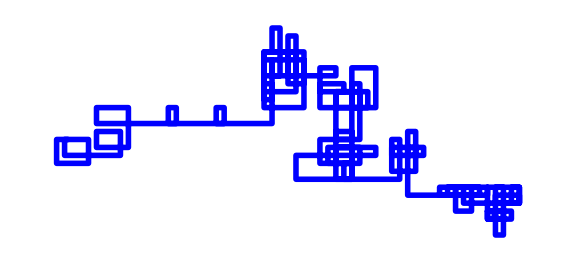

```mathematica
primeTurn[1000]
```

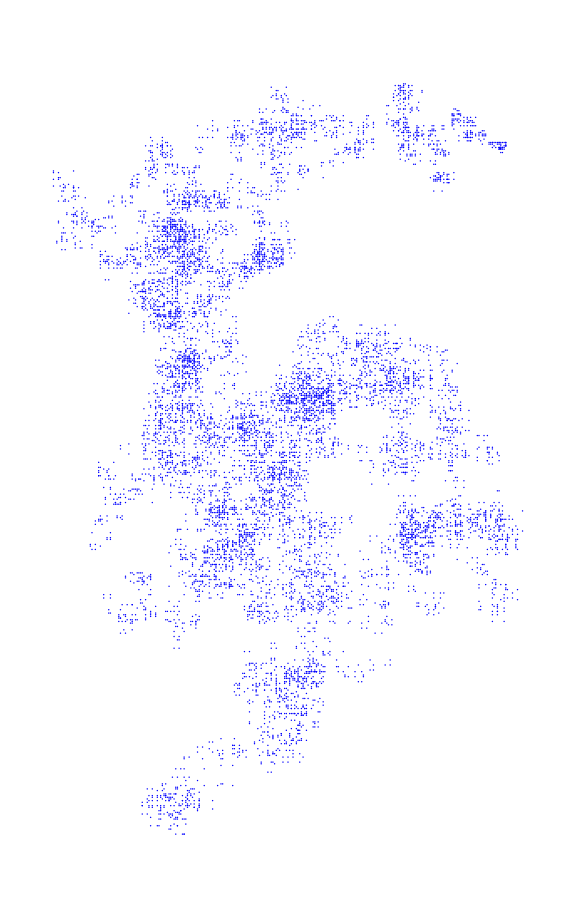

```mathematica
primeTurn[100000]
```

```mathematica
ClearAll["Global`*"]
```